# Weibull distribution

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
http://www.eugenedeon.com/hitchhikers

## Definition

```mathematica
Weibull`pc[s_,a_]:=a s^(a-1)Exp[-s^a]
```

### Normalization

```mathematica
Integrate[Weibull`pc[s,a],{s,0,Infinity},Assumptions->a>0]
```

1

### Mean

```mathematica
Integrate[Weibull`pc[s,a]s,{s,0,Infinity},Assumptions->a>0]//FullSimplify
```

Gamma[1+1/a]

### Moments

```mathematica
Integrate[Weibull`pc[s,a] s^p,{s,0,Infinity},Assumptions->p>0&&a>0]
```

Gamma[(a+p)/a]

## Laplace Representation

```mathematica
InverseLaplaceTransform[a s^(a-1)Exp[-s^a]/.a->1/2,s,x]
```

ⅇ^(-1/4/x)/(2 √π √x)

## GRT Statistics

```mathematica
Weibull`Xc[s_,a_]:=ⅇ^(-s^a)
```

```mathematica
Weibull`Σtc[s_,a_]:=a s^(-1+a)
```

```mathematica
Weibull`pu[s_,a_]:=(ⅇ^(-s^a))/Gamma[1+1/a]
```

```mathematica
Weibull`Xu[s_,a_]:=Gamma[1/a,s^a]/Gamma[1/a]
```

```mathematica
Weibull`Σtu[s_,a_]:=(a ⅇ^(-s^a))/Gamma[1/a,s^a]
```

## Fourier Propagator

```mathematica
assumps=a>0;
```

```mathematica
πd[d,Weibull`pc[r,1/2]]
```

1/(6 d z^2)Gamma[1+d/2] ((12 √2 z^(3/2) Gamma[5/4] HypergeometricPFQ[{5/4-d/2},{1/2,3/4},-1/(64 z^2)])/Gamma[-1/4+d/2]-(6 √π z HypergeometricPFQ[{3/2-d/2},{3/4,5/4},-1/(64 z^2)])/Gamma[1/2 (-1+d)]+(3 √2 √z Gamma[3/4] HypergeometricPFQ[{7/4-d/2},{5/4,3/2},-1/(64 z^2)])/Gamma[-3/4+d/2]-(2 HypergeometricPFQ[{1,2-d/2},{5/4,3/2,7/4},-1/(64 z^2)])/Gamma[-1+d/2])

```mathematica
πd[d,Weibull`pc[r,1]]
```

Hypergeometric2F1[1/2,1,d/2,-z^2]

```mathematica
πd[d,Weibull`pc[r,2]]
```

ⅈ^-d 2^(-3+d) ⅇ^(-z^2/4) z^(2-d) (-2 Gamma[d/2]+(-2+d) Gamma[-1+d/2,-z^2/4])

```mathematica
πd[d,Weibull`pc[r,3]]
```

1/(24 d)Gamma[1+d/2] (-(8 z^2 Gamma[2/3] HypergeometricPFQ[{5/6},{2/3,1/3+d/6,2/3+d/6,1+d/6},-z^6/11664])/Gamma[1+d/2]+(3^(-1/2-d/2) π z^4 Gamma[7/3] HypergeometricPFQ[{7/6},{4/3,2/3+d/6,1+d/6,4/3+d/6},-z^6/11664])/(Gamma[1+d/6] Gamma[(4+d)/6] Gamma[(8+d)/6])+(24 d HypergeometricPFQ[{1/2,1},{1/3,2/3,1/3+d/6,2/3+d/6,d/6},-z^6/11664])/Gamma[1+d/2])

## Random Variates / Importance Sampling

[Devroye 2006]

```mathematica
Weibull`samplepc[a_]:=(-Log[RandomReal[]])^(1/a)
```

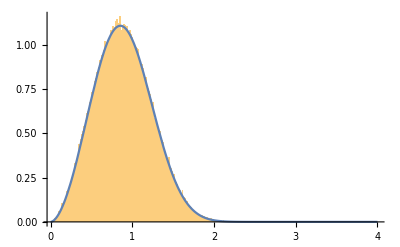

```mathematica
With[{a=2.8},
Show[
Histogram[Table[Weibull`samplepc[a],{i,Range[120000]}],300,"PDF"],
Plot[Weibull`pc[s,a],{s,0,4},PlotRange->All],
PlotRange->All
]
]
```

```mathematica
Weibull`samplepu[a_]:=InverseGammaRegularized[1/a,(-RandomReal[]+1)a Gamma[1+1/a]]^(1/a)
```

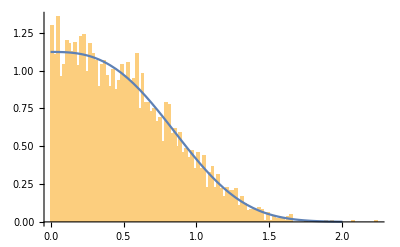

```mathematica
With[{a=2.8},
Show[
Histogram[Table[Weibull`samplepu[a],{i,Range[10220]}],100,"PDF"],
Plot[Weibull`pu[s,a],{s,0,2},PlotRange->All],
PlotRange->All
]
]
```

## Grosjean F functions in 3D

### a = 3

```mathematica
pc=c Weibull`pc[#,3]&
```

c Weibull`pc[#1,3]&

```mathematica
Fpc[0,0,pc,z]
```

c HypergeometricPFQ[{1},{1/3,2/3,5/6,7/6},-z^6/11664]-(2 c π (KelvinBer[-2/3,(2 z^(3/2))/(3 √3)]+KelvinBer[2/3,(2 z^(3/2))/(3 √3)]))/(3 √3)

```mathematica
Fpc[1,0,pc,z]
```

-1/90 c (3 z^3 HypergeometricPFQ[{1},{2/3,7/6,4/3,11/6},-z^6/11664]+20 √3 π (KelvinBei[-4/3,(2 z^(3/2))/(3 √3)]+KelvinBei[4/3,(2 z^(3/2))/(3 √3)]))

```mathematica
Fpc[1,1,pc,z]
```

1/105840 c (1176 z^2 Gamma[2/3] HypergeometricPFQ[{5/6},{2/3,7/6,3/2,11/6},-z^6/11664]-27 z^4 Gamma[10/3] HypergeometricPFQ[{7/6},{4/3,3/2,11/6,13/6},-z^6/11664]-17640 HypergeometricPFQ[{1/2,1},{1/3,2/3,5/6,7/6,3/2},-z^6/11664]-2 (1176 z^2 Gamma[2/3] HypergeometricPFQ[{5/6,4/3},{1/3,2/3,7/6,3/2,11/6},-z^6/11664]-54 z^4 Gamma[10/3] HypergeometricPFQ[{7/6,5/3},{2/3,4/3,3/2,11/6,13/6},-z^6/11664]+7 z^6 HypergeometricPFQ[{3/2,2},{4/3,5/3,11/6,13/6,5/2},-z^6/11664])+5880 (9 HypergeometricPFQ[{1},{1/3,2/3,5/6,7/6},-z^6/11664]-2 √3 π (KelvinBer[-2/3,(2 z^(3/2))/(3 √3)]+KelvinBer[2/3,(2 z^(3/2))/(3 √3)])))

```mathematica
Fpc[2,0,pc,z]
```

1/26460 c (1176 z^2 Gamma[2/3] HypergeometricPFQ[{5/6,4/3},{1/3,2/3,7/6,3/2,11/6},-z^6/11664]-54 z^4 Gamma[10/3] HypergeometricPFQ[{7/6,5/3},{2/3,4/3,3/2,11/6,13/6},-z^6/11664]+7 z^6 HypergeometricPFQ[{3/2,2},{4/3,5/3,11/6,13/6,5/2},-z^6/11664])

```mathematica
Fpc[2,1,pc,z]
```

-1/(2520 z^5)c (315 (-2)^(2/3) (1+ⅈ)^(2/3) 3^(1/6) π z^3 AiryAi[-((-1)^(1/6) z)/3^(1/3)]+1890 (-1)^(5/12) (1+ⅈ)^(5/3) 6^(1/6) π z^3 AiryAi[-((-1)^(1/6) z)/3^(1/3)]-315 (-2)^(2/3) (1+ⅈ)^(2/3) 3^(1/6) π z^3 AiryAi[((-1)^(1/6) z)/3^(1/3)]-1890 (-1)^(5/12) (1+ⅈ)^(5/3) 6^(1/6) π z^3 AiryAi[((-1)^(1/6) z)/3^(1/3)]-4410 ⅈ 3^(1/6) π z^3 AiryAi[((3+ⅈ √3) z)/(2 3^(5/6))]+4410 ⅈ 3^(1/6) π z^3 AiryAi[-(ⅈ (-3 ⅈ+√3) z)/(2 3^(5/6))]+1260 (-3)^(5/6) (1+ⅈ)^(4/3) 2^(1/3) π z AiryAiPrime[-((-1)^(1/6) z)/3^(1/3)]-11340 ⅈ 3^(5/6) π z AiryAiPrime[-((-1)^(1/6) z)/3^(1/3)]-2205 (-1)^(1/12) (1+ⅈ)^(4/3) 6^(5/6) π z AiryAiPrime[-((-1)^(1/6) z)/3^(1/3)]+2205 (-1)^(7/12) (1+ⅈ)^(4/3) 6^(5/6) π z AiryAiPrime[-((-1)^(1/6) z)/3^(1/3)]-210 3^(5/6) π z^4 AiryAiPrime[-((-1)^(1/6) z)/3^(1/3)]+105 (-2)^(1/3) (1+ⅈ)^(4/3) 3^(5/6) π z^4 AiryAiPrime[-((-1)^(1/6) z)/3^(1/3)]-1260 (-3)^(5/6) (1+ⅈ)^(4/3) 2^(1/3) π z AiryAiPrime[((-1)^(1/6) z)/3^(1/3)]+11340 ⅈ 3^(5/6) π z AiryAiPrime[((-1)^(1/6) z)/3^(1/3)]+2205 (-1)^(1/12) (1+ⅈ)^(4/3) 6^(5/6) π z AiryAiPrime[((-1)^(1/6) z)/3^(1/3)]-2205 (-1)^(7/12) (1+ⅈ)^(4/3) 6^(5/6) π z AiryAiPrime[((-1)^(1/6) z)/3^(1/3)]-210 3^(5/6) π z^4 AiryAiPrime[((-1)^(1/6) z)/3^(1/3)]+105 (-2)^(1/3) (1+ⅈ)^(4/3) 3^(5/6) π z^4 AiryAiPrime[((-1)^(1/6) z)/3^(1/3)]+5670 ⅈ (-6)^(2/3) (1+ⅈ)^(2/3) π AiryBi[-((-1)^(1/6) z)/3^(1/3)]-5670 (-1)^(11/12) (1+ⅈ)^(5/3) 2^(1/6) 3^(2/3) π AiryBi[-((-1)^(1/6) z)/3^(1/3)]-630 (-6)^(2/3) (1+ⅈ)^(2/3) π z^3 AiryBi[-((-1)^(1/6) z)/3^(1/3)]-105 (-1)^(5/12) (1+ⅈ)^(5/3) 2^(1/6) 3^(2/3) π z^3 AiryBi[-((-1)^(1/6) z)/3^(1/3)]+5670 ⅈ (-6)^(2/3) (1+ⅈ)^(2/3) π AiryBi[((-1)^(1/6) z)/3^(1/3)]-5670 (-1)^(11/12) (1+ⅈ)^(5/3) 2^(1/6) 3^(2/3) π AiryBi[((-1)^(1/6) z)/3^(1/3)]+630 (-6)^(2/3) (1+ⅈ)^(2/3) π z^3 AiryBi[((-1)^(1/6) z)/3^(1/3)]+105 (-1)^(5/12) (1+ⅈ)^(5/3) 2^(1/6) 3^(2/3) π z^3 AiryBi[((-1)^(1/6) z)/3^(1/3)]-1470 ⅈ 3^(2/3) π z^3 AiryBi[((3+ⅈ √3) z)/(2 3^(5/6))]+1470 ⅈ 3^(2/3) π z^3 AiryBi[-(ⅈ (-3 ⅈ+√3) z)/(2 3^(5/6))]+11340 ⅈ 3^(1/3) π z AiryBiPrime[-((-1)^(1/6) z)/3^(1/3)]-2205 (-1)^(1/12) (1+ⅈ)^(4/3) 2^(5/6) 3^(1/3) π z AiryBiPrime[-((-1)^(1/6) z)/3^(1/3)]+2205 (-1)^(7/12) (1+ⅈ)^(4/3) 2^(5/6) 3^(1/3) π z AiryBiPrime[-((-1)^(1/6) z)/3^(1/3)]+1260 (-1)^(5/6) (1+ⅈ)^(4/3) 6^(1/3) π z AiryBiPrime[-((-1)^(1/6) z)/3^(1/3)]+105 (-6)^(1/3) (1+ⅈ)^(4/3) π z^4 AiryBiPrime[-((-1)^(1/6) z)/3^(1/3)]+210 3^(1/3) π z^4 AiryBiPrime[-((-1)^(1/6) z)/3^(1/3)]-11340 ⅈ 3^(1/3) π z AiryBiPrime[((-1)^(1/6) z)/3^(1/3)]+2205 (-1)^(1/12) (1+ⅈ)^(4/3) 2^(5/6) 3^(1/3) π z AiryBiPrime[((-1)^(1/6) z)/3^(1/3)]-2205 (-1)^(7/12) (1+ⅈ)^(4/3) 2^(5/6) 3^(1/3) π z AiryBiPrime[((-1)^(1/6) z)/3^(1/3)]-1260 (-1)^(5/6) (1+ⅈ)^(4/3) 6^(1/3) π z AiryBiPrime[((-1)^(1/6) z)/3^(1/3)]+105 (-6)^(1/3) (1+ⅈ)^(4/3) π z^4 AiryBiPrime[((-1)^(1/6) z)/3^(1/3)]+210 3^(1/3) π z^4 AiryBiPrime[((-1)^(1/6) z)/3^(1/3)]+12 z^8 HypergeometricPFQ[{1},{1/3,2/3,11/6,13/6},-z^6/11664]+42 z^8 HypergeometricPFQ[{1},{2/3,7/6,4/3,11/6},-z^6/11664]-6 z^8 HypergeometricPFQ[{1},{2/3,4/3,11/6,13/6},-z^6/11664]+280 √3 π z^5 KelvinBei[-4/3,(2 z^(3/2))/(3 √3)]+280 √3 π z^5 KelvinBei[4/3,(2 z^(3/2))/(3 √3)])